```mathematica
DSolve[{y'[x]==((x*Exp[3*x])-2*y[x]),y[0]==0},y[x],x]
```

{{y[x]→1/25 ⅇ^(-2 x) (1-ⅇ^(5 x)+5 ⅇ^(5 x) x)}}

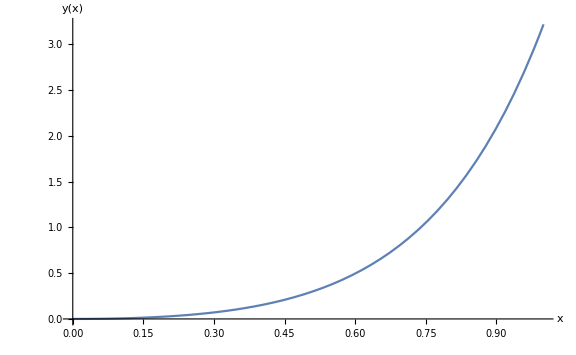

```mathematica
{{y[x]->1/25 ⅇ^(-2 x) (1-ⅇ^(5 x)+5 ⅇ^(5 x) x)}}
Plot[1/25 ⅇ^(-2 x) (1-ⅇ^(5 x)+5 ⅇ^(5 x) x),{x,0,1},ImageSize->Large,  AxesLabel->{x,"y(x)"}]
```

```mathematica
DSolve[{y'[x]==(1-(x-y[x])^2),y[2]==1},y[x],x]
```

{{y[x]→(1-3 x+x^2)/(-3+x)}}

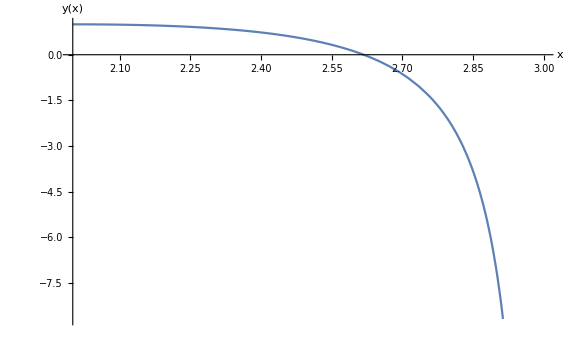

```mathematica
{{y[x]->(1-3 x+x^2)/(-3+x)}}
Plot[(1-3 x+x^2)/(-3+x),{x,2,3},  AxesLabel->{x,"y(x)"}]
```

```mathematica
DSolve[{y'[x]==(1+(y[x]/x)),y[1]==2},y[x],x]
```

{{y[x]→2 x+x Log[x]}}

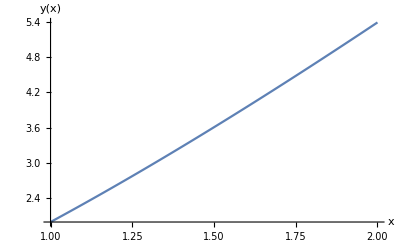

```mathematica
{{y[x]->2 x+x Log[x]}}
Plot[2 x+x Log[x],{x,1,2},  AxesLabel->{x,"y(x)"}]
```

```mathematica
DSolve[{y'[x]==Cos[2*x]+Sin[3*x],y[0]==1},y[x],x]
```

{{y[x]→1/6 (8-2 Cos[3 x]+3 Sin[2 x])}}

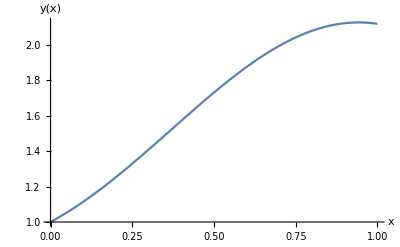

```mathematica
{{y[x]->1/6 (8-2 Cos[3 x]+3 Sin[2 x])}}
Plot[1/6 (8-2 Cos[3 x]+3 Sin[2 x]),{x,0,1},  AxesLabel->{x,"y(x)"}]
```